## Stats for de Sitter

```mathematica
data=Import["/Users/mb909/c-workspace/CausalSets/minminusmax-desitter-data.txt","Table"];
stat=Import["/Users/mb909/c-workspace/CausalSets/minminusmax-desitter-stat.txt","Table"];
```

```mathematica
stat=Transpose[{Transpose[stat][[1]],Transpose[stat][[4]]}];
```

```mathematica
stat
```

{{8,2.27332},{16,2.48487},{32,2.87735},{64,3.3003},{128,4.19874},{256,4.91218},{512,5.61975},{1024,6.37803},{2048,7.93627},{4096,9.41911},{8192,10.909},{16384,13.102},{32768,15.8589},{65536,18.5504},{131072,21.9366}}

```mathematica
f[x]=x/.{x->Fit[stat,{1,Log[x]^2},x]}
```

0.627273+0.140724 Log[x]^2

```mathematica
f[x]
```

4.04478+0.0562011 √x

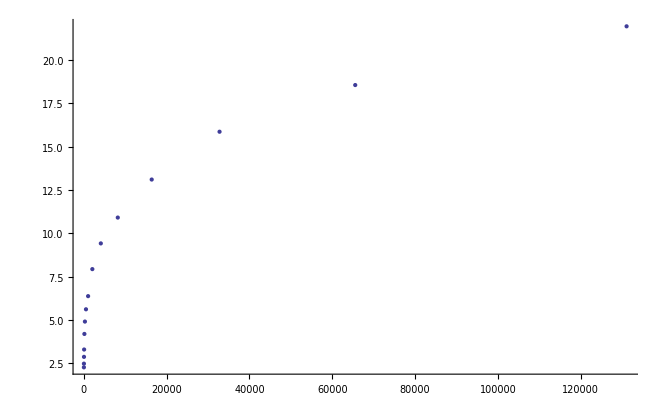

```mathematica
Show[ListPlot[stat],Plot[%,{x,0,250000}]]
```

```mathematica
data=Delete[data,1];
data=Transpose[{Log@Transpose[data][[1]],Transpose[data][[2]]}];
```

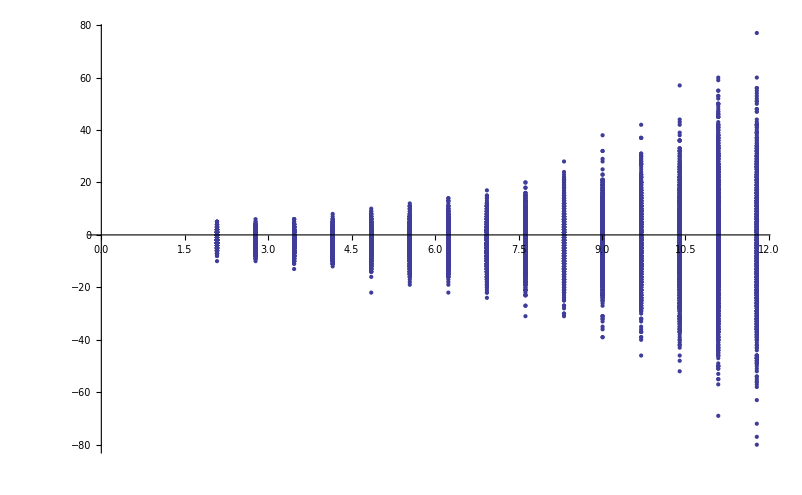

```mathematica
ListPlot[data,AxesOrigin->{0,0},PlotRange->Full]
```

## Stats for Minkowski d = 2

```mathematica
data=Import["/Users/mb909/c-workspace/CausalSets/minminusmax-mink2-data.txt","Table"];
stat=Import["/Users/mb909/c-workspace/CausalSets/minminusmax-mink2-stat.txt","Table"];
```

### Time analysis:

```mathematica
times=Transpose[{Transpose[stat][[2]],Transpose[stat][[4]]}];
```

```mathematica
Fit[times,{x,x^2},x]
```

0.00261742 x+2.50972×10^-8 x^2

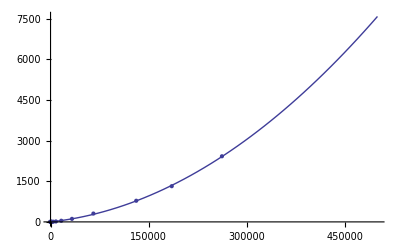

```mathematica
Show[Plot[0.00261742234860868 x+2.5097196743799026*^-8 x^2,{x,0,500000},PlotRange->Full],ListPlot[times,PlotRange->Full]]
```

### STDEV analysis:

```mathematica
stdevs=Transpose[{Transpose[stat][[2]],Transpose[stat][[-1]]}];
```

```mathematica
n=.
```

```mathematica
fit=Fit[Log@stdevs,{1,x},x]
```

-0.078685+0.237907 x

```mathematica
fit=Exp[ReplaceAll[fit,x->Log[x]]]
```

0.924331 x^0.237907

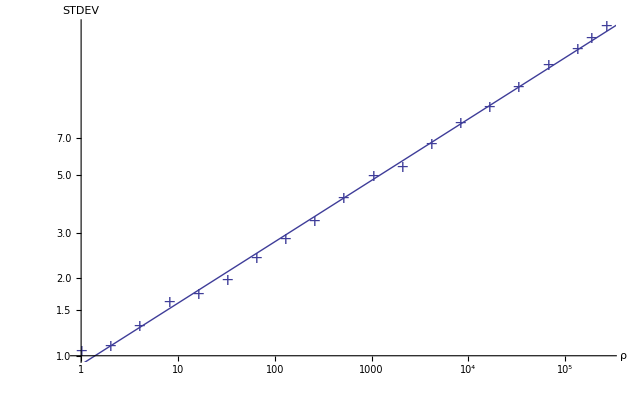

```mathematica
graph2d=Show[ListLogLogPlot[stdevs,AxesOrigin->{0,0},PlotMarkers->{"+",16},AxesLabel->{"ρ","STDEV"},PlotRange->{0,100}],LogLogPlot[fit,{x,0.01,10^6}]]
```

```mathematica
Drop[{1,2,3,4},3]
```

{4}

```mathematica
FindFit[Drop[stdevs,5],a Log[ x+c],{a,b,c},x]
```

FindFit[{{32,1.958},{64,2.38},{128,2.823},{256,3.311},{512,4.05},{1024,4.933},{2048,5.38},{4096,6.587},{8192,7.942},{16384,9.186},{32768,10.963},{65536,13.284},{131072,15.435},{262144,18.888},{185364,16.888}},Log[c+x],{1,1/2,c},x]

```mathematica
a Log[b x+c]/.%
```

1.71688 Log[106.451-6.0117 x]

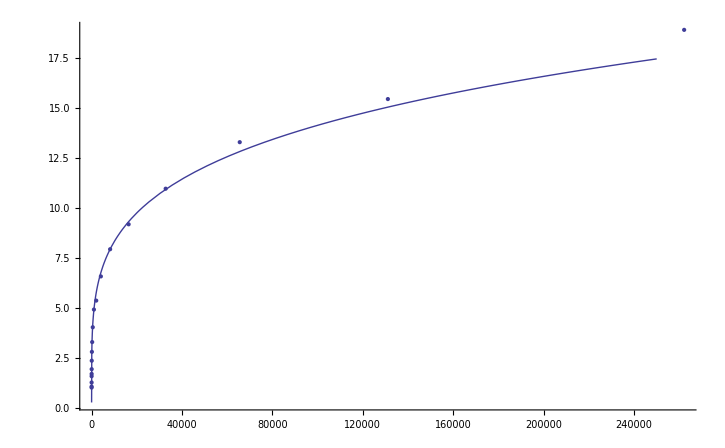

```mathematica
Show[ListPlot[stdevs],Plot[x^0.23 ,{x,0,250000}]]
```

```mathematica
data=Delete[data,1];
data=Transpose[{Log@Transpose[data][[1]],Transpose[data][[2]]}];
```

```mathematica
Mean[data]//N
```

{27594.1,-0.0212632}

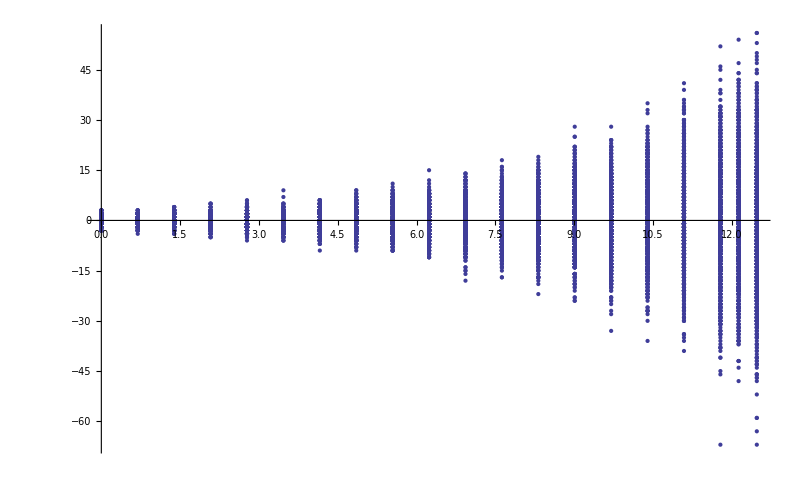

```mathematica
ListPlot[data,AxesOrigin->{0,0},PlotRange->Full]
```

## Stats for Minkowski d = 3

```mathematica
data=Import["/Users/mb909/c-workspace/CausalSets/140529minminusmax-cyl3-smeared-lk1-data.txt","Table"];
stat=Import["/Users/mb909/c-workspace/CausalSets/140529minminusmax-cyl3-smeared-lk1-stat.txt","Table"];
```

```mathematica
stat
```

{{100,16,0.006944,201.77,0.181,1.797,23.682},{100,23,0.00491,284.54,0.32,-0.034,32.238},{100,32,0.003472,400.61,0.509,-3.109,36.507},{100,45,0.002455,566.11,1.067,3.211,46.87},{100,64,0.001736,808.97,1.967,2.469,54.124},{100,91,0.001228,1134.55,3.614,0.772,58.102},{100,128,0.0008681,1604.59,7.227,4.076,76.716},{100,181,0.0006138,2273.22,14.821,-11.286,86.142},{100,256,0.000434,3215.51,28.517,-4.851,121.213},{100,362,0.0003069,4541.05,58.482,-6.305,124.842},{100,512,0.000217,6433.35,125.909,7.979,144.97},{100,724,0.0001535,9089.11,248.601,-10.162,181.533},{100,1024,0.0001085,12867.5,511.622,-33.405,213.285},{100,1448,0.00007673,18189.8,1072.,-10.795,243.29},{100,2048,0.00005425,25734.9,2182.15,-3.275,318.903},{100,2896,0.00003836,36389.9,4205.09,-61.426,342.617}}

### Time analysis:

```mathematica
times=Transpose[{Transpose[stat][[2]],Transpose[stat][[4]]}];
```

```mathematica
Fit[times,{x,x^2},x]
```

0.00261742 x+2.50972×10^-8 x^2

```mathematica
Show[Plot[0.00261742234860868 x+2.5097196743799026*^-8 x^2,{x,0,500000},PlotRange->Full],ListPlot[times,PlotRange->Full]]
```

-Graphics-

### STDEV analysis:

```mathematica
stdevs=Transpose[{Transpose[stat][[2]],Transpose[stat][[-1]]}];
```

```mathematica
stdevs
```

{{16,23.682},{23,32.238},{32,36.507},{45,46.87},{64,54.124},{91,58.102},{128,76.716},{181,86.142},{256,121.213},{362,124.842},{512,144.97},{724,181.533},{1024,213.285},{1448,243.29},{2048,318.903},{2896,342.617}}

```mathematica
n=.
```

```mathematica
x=.
```

```mathematica
fit=Fit[Log@stdevs,{1,x},x]
```

1.85444+0.506274 x

```mathematica
fit=Exp[ReplaceAll[fit,x->Log[x]]]
```

6.38812 x^0.506274

```mathematica
Norm[1-3]
```

2

```mathematica
s=CSMinkowski3Rectangle[3]
```

{{{0.737782,0.387644,0.168738},{0.416661,0.734145,0.303933},{0.864626,0.784057,0.357325}},CSMinkowski3Rectangle,3,3,1.,{1.,1.,1.}}

```mathematica
x=CSpace[s]
```

{{0.737782,0.387644},{0.416661,0.734145},{0.864626,0.784057}}

```mathematica
Map[Norm,Outer[Plus, -x, x,1],-2]
```

{0.629614,0.652952,0.613511}

```mathematica
Map[Norm,Outer[Plus, -x, x,1],0]//MatrixForm
```

((0.
0.) | (0.0838504
0.289426) | (0.219771
0.188813) | (-0.286878
0.567429) | (0.365591
0.182429) | (-0.196545
0.721243) | (-0.0707696
0.448583) | (0.261391
-0.0203062) | (-0.361295
0.19771) | (0.611788
0.659588)
(-0.0838504
-0.289426) | (0.
0.) | (0.135921
-0.100613) | (-0.370729
0.278003) | (0.281741
-0.106997) | (-0.280396
0.431817) | (-0.15462
0.159157) | (0.177541
-0.309732) | (-0.445145
-0.0917157) | (0.527938
0.370162)
(-0.219771
-0.188813) | (-0.135921
0.100613) | (0.
0.) | (-0.506649
0.378616) | (0.14582
-0.00638344) | (-0.416316
0.53243) | (-0.290541
0.25977) | (0.0416198
-0.209119) | (-0.581066
0.00889753) | (0.392017
0.470775)
(0.286878
-0.567429) | (0.370729
-0.278003) | (0.506649
-0.378616) | (0.
0.) | (0.65247
-0.385) | (0.090333
0.153814) | (0.216109
-0.118846) | (0.548269
-0.587735) | (-0.0744164
-0.369719) | (0.898667
0.0921593)
(-0.365591
-0.182429) | (-0.281741
0.106997) | (-0.14582
0.00638344) | (-0.65247
0.385) | (0.
0.) | (-0.562137
0.538813) | (-0.436361
0.266154) | (-0.1042
-0.202735) | (-0.726886
0.015281) | (0.246197
0.477159)
(0.196545
-0.721243) | (0.280396
-0.431817) | (0.416316
-0.53243) | (-0.090333
-0.153814) | (0.562137
-0.538813) | (0.
0.) | (0.125776
-0.27266) | (0.457936
-0.741549) | (-0.164749
-0.523532) | (0.808334
-0.0616546)
(0.0707696
-0.448583) | (0.15462
-0.159157) | (0.290541
-0.25977) | (-0.216109
0.118846) | (0.436361
-0.266154) | (-0.125776
0.27266) | (0.
0.) | (0.332161
-0.468889) | (-0.290525
-0.250873) | (0.682558
0.211005)
(-0.261391
0.0203062) | (-0.177541
0.309732) | (-0.0416198
0.209119) | (-0.548269
0.587735) | (0.1042
0.202735) | (-0.457936
0.741549) | (-0.332161
0.468889) | (0.
0.) | (-0.622686
0.218016) | (0.350397
0.679894)
(0.361295
-0.19771) | (0.445145
0.0917157) | (0.581066
-0.00889753) | (0.0744164
0.369719) | (0.726886
-0.015281) | (0.164749
0.523532) | (0.290525
0.250873) | (0.622686
-0.218016) | (0.
0.) | (0.973083
0.461878)
(-0.611788
-0.659588) | (-0.527938
-0.370162) | (-0.392017
-0.470775) | (-0.898667
-0.0921593) | (-0.246197
-0.477159) | (-0.808334
0.0616546) | (-0.682558
-0.211005) | (-0.350397
-0.679894) | (-0.973083
-0.461878) | (0.
0.))

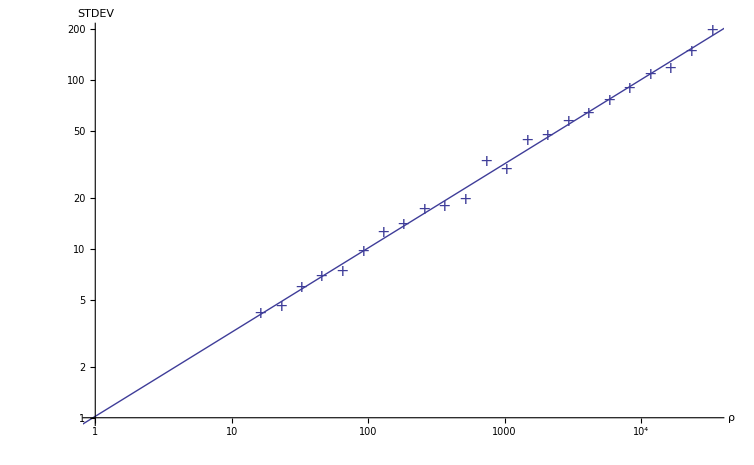

```mathematica
graph2dsmeared=Show[ListLogLogPlot[stdevs,PlotRange->{0,30},AxesOrigin->{0,0},PlotMarkers->{"+",16},AxesLabel->{"ρ","STDEV"}],LogLogPlot[fit,{x,0.00001,10^6}]]
```

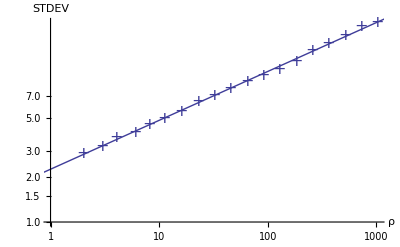

```mathematica
Show@%
```

```mathematica
FindFit[Drop[stdevs,5],a Log[ x+c],{a,b,c},x]
```

FindFit[{{32,1.958},{64,2.38},{128,2.823},{256,3.311},{512,4.05},{1024,4.933},{2048,5.38},{4096,6.587},{8192,7.942},{16384,9.186},{32768,10.963},{65536,13.284},{131072,15.435},{262144,18.888},{185364,16.888}},Log[c+x],{1,1/2,c},x]

```mathematica
a Log[b x+c]/.%
```

1.71688 Log[106.451-6.0117 x]

```mathematica
Show[ListPlot[stdevs],Plot[x^0.23 ,{x,0,250000}]]
```

-Graphics-

```mathematica
data=Delete[data,1];
data=Transpose[{Log@Transpose[data][[1]],Transpose[data][[2]]}];
```

```mathematica
Mean[data]//N
```

{27594.1,-0.0212632}

```mathematica
ListPlot[data,AxesOrigin->{0,0},PlotRange->Full]
```

-Graphics-

```mathematica
{t,T-x}
```

{t,T-x}

```mathematica
VectorPlot[{-t,1-x},{x,-1,1},{t,-1,1},AxesLabel->{"x","t"}]
```

```mathematica
0.8^5
```

0.32768

```mathematica
r0=.
```

```mathematica
int=Integrate[(2 t^2+r0^2)/(t^2+r0^2),t]
```

2 t-r0 ArcTan[t/r0]

```mathematica
ReplaceAll[int,t->T]-ReplaceAll[int,t->0]//FullSimplify
```

2 T-r0 ArcTan[T/r0]

```mathematica
}
```

```mathematica
650*12/52
```

150

```mathematica
ϵ
```

```mathematica
\footnote{The independence is as a feature of the Poisson process in $M$:the number of elements $N(R)$ in any subregion $R\subset M$ is a Poisson variable itself,and for any two disjoint regions $R_1$,$R_2$ the numbers $N(R_1)$ and $N(R_2)$ are independent random variables.}
```

## Stats for Minkowski d = 4

```mathematica
data=Import["/Users/mb909/c-workspace/CausalSets/2014-05-30-11-46-48-minminusmax-mink4-data.txt","Table"];
stat=Import["/Users/mb909/c-workspace/CausalSets/2014-05-30-11-46-48-minminusmax-mink4-stat.txt","Table"];
```

```mathematica
stat
```

{{100,2,2.44,0.003,0.014,0.899},{100,3,2.43,0.003,-0.071,0.693},{100,4,4.06,0.004,0.085,0.832},{100,6,4.18,0.004,0.088,0.771},{100,8,8.35,0.006,0.092,0.94},{100,11,10.16,0.007,-0.048,0.842},{100,16,15.67,0.009,-0.122,0.866},{100,23,22.39,0.012,-0.09,0.747},{100,32,31.78,0.016,-0.039,0.779},{100,45,43.95,0.022,0.012,0.751},{100,64,65.52,0.034,-0.037,0.732},{100,91,88.64,0.047,0.052,0.684},{100,128,128.32,0.072,-0.142,0.679},{100,181,180.83,0.091,0.018,0.593},{100,256,255.22,0.14,0.081,0.544},{100,362,363.03,0.255,-0.047,0.543},{100,512,511.41,0.438,0.079,0.452},{100,724,727.54,0.67,-0.016,0.457},{100,1024,1024.78,0.802,0.007,0.433},{100,1448,1451.79,1.323,0.001,0.402},{100,2048,2046.64,2.376,-0.021,0.402},{100,2896,2893.98,4.254,0.054,0.456},{100,4096,4096.81,7.1,0.013,0.358},{100,5793,5799.04,12.492,-0.001,0.401},{100,8192,8187.75,22.038,-0.002,0.358},{100,11585,11584.8,42.458,0.05,0.331},{100,16384,16372.,94.046,0.,0.31}}

### Time analysis:

```mathematica
times=Transpose[{Transpose[stat][[2]],Transpose[stat][[4]]}];
```

```mathematica
fit=FindFit[Log@times,{1,x},x]
```

-7.74871+1.1505 x

```mathematica
fit=Exp[ReplaceAll[fit,x->Log[x]]]
```

0.000431297 x^1.1505

```mathematica
graph2dsmeared=Show[ListLogLogPlot[stdevs,PlotRange->{0,30},AxesOrigin->{0,0},PlotMarkers->{"+",16},AxesLabel->{"ρ","STDEV"}],LogLogPlot[fit,{x,0.00001,10^6}]]
```

```mathematica
fit=Function[x,Evaluate@Fit[times,{x,x^2},x]]
```

Function[x,-0.0000375339 x+3.46249×10^-7 x^2]

```mathematica
fit[y]
```

-0.0000375339 y+3.46249×10^-7 y^2

```mathematica
Max@times[[2,All]]
```

3

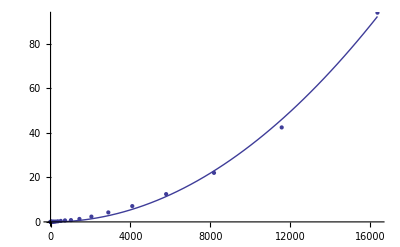

```mathematica
Show[Plot[fit[x],{x,0,Max@times[[All,1]]},PlotRange->Full],ListPlot[times,PlotRange->Full]]
```

### STDEV analysis:

```mathematica
stdevs=Transpose[{Transpose[stat][[2]],Transpose[stat][[-1]]}];
```

```mathematica
stdevs
```

{{2,0.899},{3,0.693},{4,0.832},{6,0.771},{8,0.94},{11,0.842},{16,0.866},{23,0.747},{32,0.779},{45,0.751},{64,0.732},{91,0.684},{128,0.679},{181,0.593},{256,0.544},{362,0.543},{512,0.452},{724,0.457},{1024,0.433},{1448,0.402},{2048,0.402},{2896,0.456},{4096,0.358},{5793,0.401},{8192,0.358},{11585,0.331},{16384,0.31}}

```mathematica
n=.
```

```mathematica
x=.
```

```mathematica
fit=Fit[Log@stdevs,{1,x},x]
```

0.0641353-0.120614 x

```mathematica
fit=Exp[ReplaceAll[fit,x->Log[x]]]
```

1.06624/x^0.120614

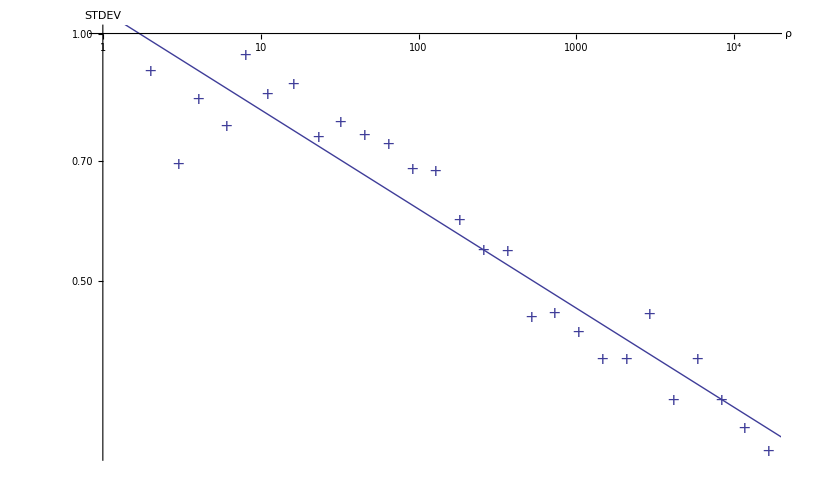

```mathematica
graph2dsmeared=Show[ListLogLogPlot[stdevs,PlotRange->{0,30},AxesOrigin->{0,0},PlotMarkers->{"+",16},AxesLabel->{"ρ","STDEV"}],LogLogPlot[fit,{x,0.00001,10^6}]]
```